## Load data

```mathematica
SetDirectory["/Users/xaq/Lab/People/Alumni/Qianli/Analyses/Summarized Code/"];
```

```mathematica
matlabData=Import["CC_test_AllData.mat","Data"];
namesraw=Import["CC_test_AllData.mat","Labels"];
```

```mathematica
namesMmca=StringReplace[#,RegularExpression["[_]"]~~x_->ToUpperCase[x]]&/@namesraw;
names=ToExpression/@namesMmca;
MapThread[Set,{names,matlabData}];
```

```mathematica
TableForm[namesMmca]
```

## Color-coded by significance

### Linear scale

```mathematica
pColor[p_,a_:1.,color_:Red]:=Blend[{GrayLevel[.8],color},Abs[2p-1]^a]
```

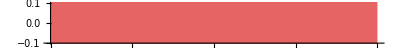

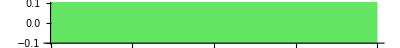

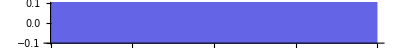

```mathematica
Plot[0,{x,0,1},ColorFunction->(pColor[#1,3.,Red]&),PlotStyle->Thickness[.2],PlotRange->{{0,1},{-.1,.1}},AxesOrigin->{0,-.1},AspectRatio->1/20,Axes->{True,False}]
Plot[0,{x,0,1},ColorFunction->(pColor[#1,3.,Green]&),PlotStyle->Thickness[.2],PlotRange->{{0,1},{-.1,.1}},AxesOrigin->{0,-.1},AspectRatio->1/20,Axes->{True,False}]
Plot[0,{x,0,1},ColorFunction->(pColor[#1,3.,Blue]&),PlotStyle->Thickness[.2],PlotRange->{{0,1},{-.1,.1}},AxesOrigin->{0,-.1},AspectRatio->1/20,Axes->{True,False}]
```

### Log color scale (use this)

Make color increments as .9, .99, .999, etc. with gray at 0.5.

```mathematica
Clear[pLogColor]
```

```mathematica
pLog[p_]:=-Log[10.,.5-Abs[p-.5]]
pLogColor[0.,pmax_,pmin_,color_:Red]:=color
pLogColor[1.,pmax_,pmin_,color_:Red]:=color
pLogColor[Indeterminate,pmax_,pmin_,color_:Red]:=White
pLogColor[p_,pmax_:.999,pmin_:.8,color_:Red]:=Blend[{GrayLevel[.8],color},(-pLog[p]+pLog[pmin])/(-pLog[pmax]+pLog[pmin])]
```

#### Colorbar

```mathematica
α=5.;d=.005;colorL={Red,Green,Blue};
colorbars=Graphics[
Table[
{pLogColor[1-10^-x,.999,.8,colorL⟦i⟧],Rectangle[{x-d/2,i-1},{x+d/2,i}]},{x,-Log[10.,.5],3.,d},{i,3}],AspectRatio->1/10,Axes->{True,False},Ticks->{{{0,0},{-Log[10.,.5],.5},{1,.9},{2,.99},{3,.999}},Automatic}]
```

### Definition of Graded Histogram

```mathematica
Clear[GradedHistogram]
```

```mathematica
GradedHistogram[xL_,pL_,nb_:9,{pmax_:.99,pmin_:.8},color_:Red,opts___]:=Module[{qdata,pos,qgrouped,pgrouped,psorted,n,ydata,δ},
n=Length[xL];δ=Differences[MinMax[xL]]⟦1⟧/(nb-1);
qdata=Round[xL,δ];
pos=Flatten[Position[qdata,#]]&/@Round[Range[Min[qdata],Max[qdata],δ],δ];
qgrouped=Part[qdata,#]&/@pos;
pgrouped=Part[pL,#]&/@pos;
psorted=Reverse/@(SortBy[#,Abs[#-.5]&]&)/@pgrouped;
ydata=(Range[Length[#]]&/@psorted)/n;
Graphics[Table[{pLogColor[psorted⟦i,j⟧,pmax,pmin,color],Rectangle[{qgrouped⟦i,j⟧-δ/2,ydata⟦i,j⟧-1/n},{qgrouped⟦i,j⟧+δ/2,ydata⟦i,j⟧}]},{i,Length[pos]},{j,Length[pos⟦i⟧]}],opts]
]
```

```mathematica
GradedLogHistogram[xL_,pL_,nb_:9,{pmax_:.99,pmin_:.8},color_:Red,opts___]:=Module[{qdata,pos,qgrouped,pgrouped,psorted,n,ydata,δ},
n=Length[xL];δ=Differences[MinMax[xL]]⟦1⟧/(nb-1);
qdata=Round[xL,δ];
pos=Flatten[Position[qdata,#]]&/@Round[Range[Min[qdata],Max[qdata],δ],δ];
qgrouped=Part[qdata,#]&/@pos;
pgrouped=Part[pL,#]&/@pos;
psorted=Reverse/@(SortBy[#,Abs[#-.5]&]&)/@pgrouped;
ydata=(Range[Length[#]]&/@psorted)/n;
Graphics[Table[{pLogColor[psorted⟦i,j⟧,pmax,pmin,color],Rectangle[{qgrouped⟦i,j⟧-δ/2,Log[ydata⟦i,j⟧-(1-10^-3.)/n]},{qgrouped⟦i,j⟧+δ/2,Log[ydata⟦i,j⟧]}]},{i,Length[pos]},{j,Length[pos⟦i⟧]}],opts]
]
```

### Plot all marginal histogram data

```mathematica
shuf=1;monk=1;monk2=2;
α={.999,.8};
iL1=RandomSample[Range[Length[ccSim2CrossF⟦shuf,monk,1⟧]],40000];
iL2=RandomSample[Range[Length[ccSim2CrossF⟦shuf,monk2,1⟧]],40000];
optseq={Axes->{False,False},Ticks->{.25{-1,1},None},AspectRatio->1/3,PlotRange->{{-.3,.3},{0,All}}};
hists2=GraphicsGrid[
{{
GradedHistogram[ccSim1F⟦shuf,monk,1⟧,pSignificantSim1F⟦shuf,monk,1⟧,32,α,Blue,Sequence@@optseq],
GradedHistogram[ccSim2SquareF⟦shuf,monk,1⟧,pSignificantSim2sqF⟦shuf,monk,1⟧,32,α,Green,Sequence@@optseq],
GradedHistogram[ccSim2CrossF⟦shuf,monk,1,iL1⟧,pSignificantSim2crF⟦shuf,monk,1,iL1⟧,32,α,Red,Sequence@@optseq],
GradedHistogram[ccSim1F⟦shuf,monk2,1⟧,pSignificantSim1F⟦shuf,monk2,1⟧,32,α,Blue,Sequence@@optseq],
GradedHistogram[ccSim2SquareF⟦shuf,monk2,1⟧,pSignificantSim2sqF⟦shuf,monk2,1⟧,32,α,Green,Sequence@@optseq],
GradedHistogram[ccSim2CrossF⟦shuf,monk2,1,iL2⟧,pSignificantSim2crF⟦shuf,monk2,1,iL2⟧,32,α,Red,Sequence@@optseq]
},{
GradedHistogram[ccTheo1F⟦shuf,monk,1⟧,pSignificantTheo1F⟦shuf,monk,1⟧,32,α,Blue,Sequence@@optseq],
GradedHistogram[ccTheo2SquareF⟦shuf,monk,1⟧,pSignificantTheo2sqF⟦shuf,monk,1⟧,32,α,Green,Sequence@@optseq],
GradedHistogram[ccTheo2CrossF⟦shuf,monk,1,iL1⟧,pSignificantTheo2crF⟦shuf,monk,1,iL1⟧,32,α,Red,Sequence@@optseq],
GradedHistogram[ccTheo1F⟦shuf,monk2,1⟧,pSignificantTheo1F⟦shuf,monk2,1⟧,32,α,Blue,Sequence@@optseq],
GradedHistogram[ccTheo2SquareF⟦shuf,monk2,1⟧,pSignificantTheo2sqF⟦shuf,monk2,1⟧,32,α,Green,Sequence@@optseq],
GradedHistogram[ccTheo2CrossF⟦shuf,monk2,1,iL2⟧,pSignificantTheo2crF⟦shuf,monk2,1,iL2⟧,32,α,Red,Sequence@@optseq]
}}ᵀ
,Spacings->0]
```